# Exercise 4

As with all of the exercises you will complete in this course, you will be expected to turn your *.nb file in to the course TA before the next lecture.  Please do so by e-mailing your completed exercise file to Lan Yu (ece329.uiuc@gmail.com), make sure you name the file using the following notation: “Exn_Last_First.nb”, where n is the Exercise number (in this case, 4), and First and Last would be your first and last name.  So my submission to Lan for this exercise would be titled “Ex4_Wasserman_Dan.nb”.  You will receive full credit for your exercise if it turned in before the next lecture (Lecture n+1).  No late submissions will be accepted.

## Objective/Overview:

In today’s exercise, we will practice Div, Grad and Curls of vector fields, as well as learn how to take surface and volume integrals.

```mathematica
ClearAll[eps0,eslab,slab2D,W,rho,diveslab2D,p1,p2,p3,p4,e1,dive1,curle1,ersphere,espherexyz, etest, rhotest, divetest,etestv,sx1,sx2,sy1,sy2,sz1,sz2]
```

## The Divergence

As we learned in class, the Divergence acts on a vector field and returns a scalar quantity which is the change in flux per unit volume.  In other words, the Divergence of a vector field tells us whether we have a source of field (E⃗) at some point in space (∇E⃗>0)  or a sink for the field (∇E⃗<0).  Let’s use our expression for a slab of charge (W=1, rho=2ϵ_o) to generate an Electric Field:

```mathematica
eps0=8.85*10^-12;rho=2*eps0; W=1;
eslab={0,0,Piecewise[{{z*rho/(eps0),Abs[z]<W/2},{Sign[z]*rho/(2*eps0),Abs[z]≥W/2}}]}
```

{0,0,Piecewise[{{2. z, Abs[z]<1/2}, {1. Sign[z], Abs[z]≥1/2}, {0, True}}]}

```mathematica
VectorPlot3D[eslab,{x,-1,1},{y,-1,1},{z,-1,1}]
```

-Graphics3D-

We should be able to take the divergence of our electric field

```mathematica
Div[eslab,{x,y,z}]
```

Piecewise[{{2., Abs[z]<1/2}, {1. Sign'[z], True}}]

We can see that this gives us a value of “2” inside the slab, and “0” outside, which make sense since we know that the divergence of ϵ_oE⃗ should give us charge density.

OK, let’s try to look at different vector fields.   Obviously we can do this in 3D if we want, but for now, let’s try to stay in 2D.  Create a 2D vector field:

```mathematica
e1={3*x,Sin[x]*y^2};
```

The divergence of this field is:

```mathematica
dive1=Div[e1,{x,y}]
```

3+2 y Sin[x]

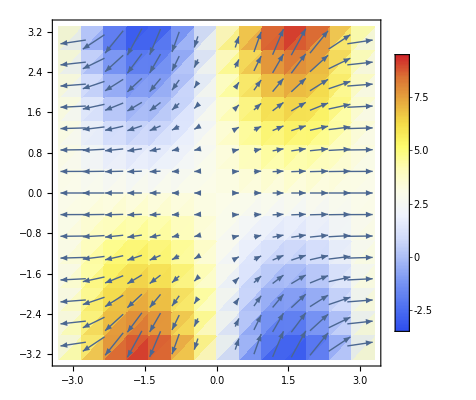

```mathematica
VectorDensityPlot[{e1,dive1},{x,-3,3},{y,-3,3}, ColorFunction->"TemperatureMap",PlotLegends->Automatic]
```

Let’s make sure we understand Divergence before we move on.  The divergence gives us the change of the vector field with position, in the direction of that position.  The scale of the divergence is simply how fast the field is changing...Let’s look at the same plot as above, but instead, look at the absolute value of the divergence..

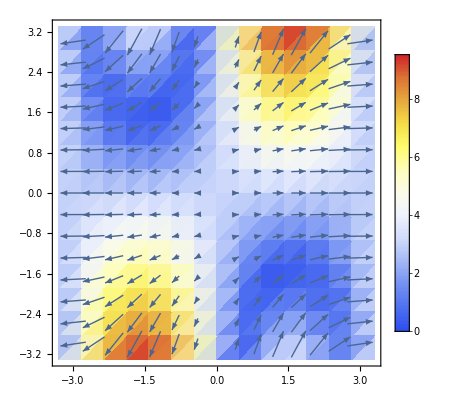

```mathematica
VectorDensityPlot[{e1,Abs[dive1]},{x,-3,3},{y,-3,3}, ColorFunction->"TemperatureMap",PlotLegends->Automatic]
```

The bluest regions correspond to points where the divergence is smallest.  We can see that these regions can occur where the vector field is changing rapidly, as long as the field is NOT changing in the direction of the vector.  In other words, if the vectors in your field are changing MAGNITUDE but NOT DIRECTION, your Divergence will be large.  If however, they are changing direction, but not magnitude, your Divergence will be small...but your Curl (we’ll get to this next!)....

Below, create a 2D Electric Field (e2) and take the divergence of your field.  Plot both the vector field and the divergence on the same axes.

```mathematica
e2={y/(Cos[x]+2),Sin[y]}
```

{y/(2+Cos[x]),Sin[y]}

```mathematica
dive2=Div[e2,{x,y}]
```

Cos[y]+(y Sin[x])/(2+Cos[x])^2

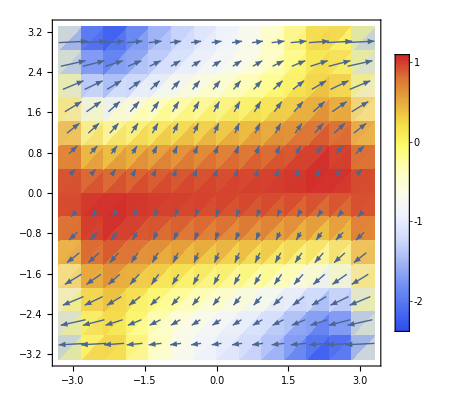

```mathematica
VectorDensityPlot[{e2,dive2},{x,-3,3},{y,-3,3}, ColorFunction->"TemperatureMap",PlotLegends->Automatic]
```

## The Curl

As we learned in class, the Curl describes the rate of change of the vector field in directions away from the direction of the vector.  The Curl of a vector field returns another Vector Field!!  This is because your Curl describes not only how fast the field is “curling”, but in what diretion! 
So let’s look at the field “e1” we used above.  Take a look at the Vector Field we plotted above first, and see if you can guess where the Curl will be largest.
Now we can take the Curl of “e1”:

```mathematica
curle1=Curl[e1,{x,y}]  (*Please bear in mind that a 2D Vector field (in x,y) will always have a Curl in the z direction, so when Mathematica takes the curl of a 2D Vector, it doesn't even bother to return a vector field, it returns the z-component of the field*)
```

y^2 Cos[x]

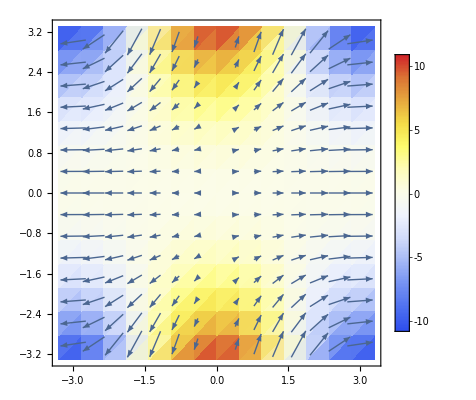

```mathematica
VectorDensityPlot[{e1,curle1},{x,-3,3},{y,-3,3}, ColorFunction->"TemperatureMap",PlotLegends->Automatic]
```

Very cool!  The bright colors line up with the regions where your vectors are turning (rotating) the fastest.  Before we move on, try one more thing:  trace the vector field in the upper right hand corner of the plot with the fingers of your right hand (have your fingertips follow the direction of the vectors.  Where is your thumb pointing?  It should be pointing into the page, or in the NEGATIVE z direction!  You will notice that the magnitude of the Curl is negative here.  What about at the bottom center of the plot?    It’s hard to see, since the vectors are getting small here, but if you trace with your right hand, you see that your thumb will point in the positive z direction!!  
You should also note that along the x-axis, your curl is basically zero, even though the vectors are changing size.  This is because they are not changing direction, or “curling”...
Below, take the Vector Field that you created above (for the Divergence exercise) and find its Curl.  Is the Curl non-zero anywhere?  Does that make sense to you?  If the Curl is zero everywhere, change your expression for the field so that the Curl is non-zero...

```mathematica
curle2=Curl[e2,{x,y}]
```

-1/(2+Cos[x])

```mathematica
e3={x/(Cos[x]+2),Sin[y]}
curle3=Curl[e3,{x,y}]
```

{x/(2+Cos[x]),Sin[y]}

0

We learned in class that ANY static Electric Field obtained from Coloumb’s Law, will be Curl-free.  Let’s take one of the fields that we have constructed in our previous exercises, and demonstrate this:

```mathematica
ersphere=Piecewise[{{rho*r/(3*eps),r<ro},{rho*ro^3/(eps*3*r^2),r≥ro}}]
```

Piecewise[{{0.666667 r, r<1}, {0.666667/r^2, r≥1}, {0, True}}]

Our vector field has only components in the r direction, and these only depend on “r”, so the field should be Curl-free.  Let’s double check:

```mathematica
Curl[{ersphere,0,0},{r,θ,ϕ},"Spherical"]
```

{0,0,0}

Can we take the Curl in cartesian coordinates?

```mathematica
esphere={ersphere,0,0}
```

{Piecewise[{{0.666667 r, r<1}, {0.666667/r^2, r≥1}, {0, True}}],0,0}

```mathematica
espherexyz=TransformedField["Spherical"->"Cartesian",esphere,{r,theta,phi}->{x,y,z}]
```

{(x (Piecewise[{{0.666667 √(x^2+y^2+z^2), √(x^2+y^2+z^2)<1}, {0.666667/(x^2+y^2+z^2), √(x^2+y^2+z^2)≥1}, {0, True}}]))/(√(x^2+y^2+z^2)),(y (Piecewise[{{0.666667 √(x^2+y^2+z^2), √(x^2+y^2+z^2)<1}, {0.666667/(x^2+y^2+z^2), √(x^2+y^2+z^2)≥1}, {0, True}}]))/(√(x^2+y^2+z^2)),(z (Piecewise[{{0.666667 √(x^2+y^2+z^2), √(x^2+y^2+z^2)<1}, {0.666667/(x^2+y^2+z^2), √(x^2+y^2+z^2)≥1}, {0, True}}]))/(√(x^2+y^2+z^2))}

```mathematica
Curl[espherexyz,{x,y,z}]
```

{(z (Piecewise[{{(0.666667 y)/(√(x^2+y^2+z^2)), √(x^2+y^2+z^2)<1}, {-(1.33333 y)/((x^2+y^2+z^2)^2), √(x^2+y^2+z^2)≥1}, {0, True}}]))/(√(x^2+y^2+z^2))-(y (Piecewise[{{(0.666667 z)/(√(x^2+y^2+z^2)), √(x^2+y^2+z^2)<1}, {-(1.33333 z)/((x^2+y^2+z^2)^2), √(x^2+y^2+z^2)≥1}, {0, True}}]))/(√(x^2+y^2+z^2)),-(z (Piecewise[{{(0.666667 x)/(√(x^2+y^2+z^2)), √(x^2+y^2+z^2)<1}, {-(1.33333 x)/((x^2+y^2+z^2)^2), √(x^2+y^2+z^2)≥1}, {0, True}}]))/(√(x^2+y^2+z^2))+(x (Piecewise[{{(0.666667 z)/(√(x^2+y^2+z^2)), √(x^2+y^2+z^2)<1}, {-(1.33333 z)/((x^2+y^2+z^2)^2), √(x^2+y^2+z^2)≥1}, {0, True}}]))/(√(x^2+y^2+z^2)),(y (Piecewise[{{(0.666667 x)/(√(x^2+y^2+z^2)), √(x^2+y^2+z^2)<1}, {-(1.33333 x)/((x^2+y^2+z^2)^2), √(x^2+y^2+z^2)≥1}, {0, True}}]))/(√(x^2+y^2+z^2))-(x (Piecewise[{{(0.666667 y)/(√(x^2+y^2+z^2)), √(x^2+y^2+z^2)<1}, {-(1.33333 y)/((x^2+y^2+z^2)^2), √(x^2+y^2+z^2)≥1}, {0, True}}]))/(√(x^2+y^2+z^2))}

Ooof, a mess.  Let’s ask Mathematica to simplify this:

```mathematica
Simplify[%]
```

{0.,0.,0.}

Huzzah!

### Putting it All Together

We know that the Divergence tells us how much field is lost or gained at a point in space.  If the Div is positive, we have a source of field, if negative, we have a sink.  We also kow that the sources and sinks of electric field lines are positive and negative charges, respectively.  This provides us with a link between the Divergence of the electric field (charge) and the flux of the electric field.  We also know that to get a static Electric field, we can take the gradient of a scalar (more on this in Exercise 5):

```mathematica
etest=Grad[y*x^2+2z*y,{x,y,z}]
```

{2 x y,x^2+2 z,2 y}

So here is our electric field.  Show that it is Curl-Free:

```mathematica
Curl[etest,{x,y,z}]
```

{0,0,0}

From this electric field, calculate the charge density

```mathematica
rhotest=Div[etest,{x,y,z}]
```

2 y

We now have the expression for charge density as a function of position.  Because we already have the Electric field, we should be able to use the E-field to calculate the flux through any closed surface.  We can then compare this to the volume integral of charge inside that same surface...
Surface integrals are actually rather tricky in Mathematica, and there is really no simple way to tell Mathematica to find the flux of a Vector field over some arbitrary surface.  You generally need to parametrize the surface, solve for the surface normal vector as a function of position on the surface, and then integrate the dot product of the vector field with your surface normal vector.  Let’s simplify things a bit here.  We can create a box, and solve the surface flux through each side of the box.
So if our box is centered at the origin, with sides of length 2:

```mathematica
p3=Graphics3D[{Opacity[0.2],Cuboid[{-1,-1,-1},{1,1,1}]}];
p4=VectorPlot3D[etest,{x,-1,1},{y,-1,1},{z,-1,1}];
```

```mathematica
Show[p3,p4]
```

-Graphics3D-

We can start with the sides facing in the + and - x directions, and remember to treat the surface normal vector dS as always pointing out!
∫_-1^1 ∫_-1^1 E⃗(x=1,y,z)·ⅆ S⃗=∫_-1^1 ∫_-1^1 E⃗(x=1,y,z)·ⅆyⅆz x̂ for the side facing the +x̂ direction and
-∫_-1^1 ∫_-1^1 E⃗(x=-1,y,z)·ⅆ S⃗=-∫_-1^1 ∫_-1^1 E⃗(x=-1,y,z)·ⅆyⅆz x̂ for the side facing the -x̂ direction

Let’s define our Vector Field

```mathematica
etestv[x_,y_,z_]=etest
```

{2 x y,x^2+2 z,2 y}

```mathematica
sx1=Integrate[Dot[etestv[1,y,z] ,{1,0,0}],{y,-1,1},{z,-1,1}] (*For the side facing +x direction*)
```

0

```mathematica
sx2=Integrate[Dot[etestv[-1,y,z],{-1,0,0}],{y,-1,1},{z,-1,1}] (*For the side facing -x direction*)
```

0

We can do the same for the y-facing sides:

```mathematica
sy1=Integrate[Dot[etestv[x,1,z],{0,1,0}],{x,-1,1},{z,-1,1}] (*For the side facing +y direction*)
```

4/3

```mathematica
sy2=Integrate[Dot[etestv[x,-1,z],{0,-1,0}],{x,-1,1},{z,-1,1}] (*For the side facing -y direction*)
```

-4/3

And finally, the z-facing sides:

```mathematica
sz1=Integrate[Dot[etestv[x,y,1],{0,0,1}],{x,-1,1},{y,-1,1}] (*For the side facing +z direction*)
```

0

```mathematica
sz2=Integrate[Dot[etestv[x,y,-1],{0,0,-1}],{x,-1,1},{y,-1,1}] (*For the side facing -z direction*)
```

0

Finding the total flux is just adding the flux through each wall ofthe cube:

```mathematica
totalflux=sx1+sx2+sy1+sy2+sz1+sz2
```

0

We should get the same thing if we integrate the divergence of epso*etest over the volume of the box.  Let’s try:

```mathematica
divetest[x_,y_,z_]=Div[etest,{x,y,z}]
```

2 y

```mathematica
Integrate[eps0*divetest[x,y,z],{x,-1,1},{y,-1,1},{z,-1,1}]
```

0

OK.  Now it’s your turn.  Take the same field, and show that the surface integral of the Electric Field flux across a box with sides of length 2, centered at {1,1,1}, is equal to the volume integral of the Divergence in that same box.  Feel free to copy and paste from above, but you will need to know how to adjust each of the expression to get the right answer.

```mathematica
p3=Graphics3D[{Opacity[0.2],Cuboid[{0,0,0},{2,2,2}]}];
p4=VectorPlot3D[etest,{x,0,2},{y,0,2},{z,0,2}];
```

```mathematica
Show[p3,p4]
```

-Graphics3D-

Let’s define our Vector Field

```mathematica
etestv[x_,y_,z_]=etest
```

{2 x y,x^2+2 z,2 y}

```mathematica
Integrate[Dot[etestv[2,y,z] ,{1,0,0}],{y,0,2},{z,0,2}] (*For the side facing +x direction*)
```

16

```mathematica
Integrate[Dot[etestv[0,y,z],{-1,0,0}],{y,0,2},{z,0,2}] (*For the side facing -x direction*)
```

0

We can do the same for the y-facing sides:

```mathematica
Integrate[Dot[etestv[x,2,z],{0,1,0}],{x,0,2},{z,0,2}] (*For the side facing +y direction*)
```

40/3

```mathematica
Integrate[Dot[etestv[x,0,z],{0,-1,0}],{x,0,2},{z,0,2}] (*For the side facing -y direction*)
```

-40/3

And finally, the z-facing sides:

```mathematica
Integrate[Dot[etestv[x,y,2],{0,0,1}],{x,0,2},{y,0,2}] (*For the side facing +z direction*)
```

8

```mathematica
Integrate[Dot[etestv[x,y,0],{0,0,-1}],{x,0,2},{y,0,2}] (*For the side facing -z direction*)
```

-8

We should get the same thing if we integrate the divergence of epso*etest over the volume of the box.  Let’s try:

```mathematica
divetest[x_,y_,z_]=Div[etest,{x,y,z}]
```

2 y

```mathematica
Integrate[divetest[x,y,z],{x,0,2},{y,0,2},{z,0,2}]
```

16